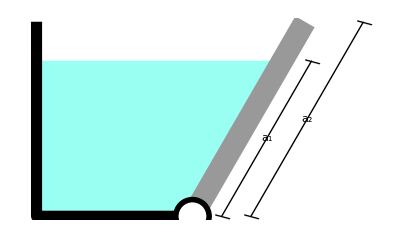

```mathematica
Module[{θ,h1,w1,w2,w3,h,a2,col,δ1,δ2},
θ=60°;
h1=4;h=5;a2=8;
w1=4;w2=h/Tan[θ];w3=h1/Tan[θ];
col=RGBColor[0.6,1,0.95];
δ1=0.75;δ2=0.1;

Graphics[{
{FaceForm@col,Polygon[{{0,h1},{0,0},{w1,0},{w1+h1/Sin[θ]*Cos[θ],h1}}]},
{Thickness@0.02,Line[{{0,h},{0,0},{w1,0}}]},
{Thickness@0.04,GrayLevel@0.6,CapForm@"Round",Line[{{w1,0},{w1+w2,h}}]},
{PointSize@0.07,Point@#,White,PointSize@0.05,Point@#}&@{w1,0},

Line[{{w1+δ1,0},{w1+w3+δ1,h1}}],
Text[Rotate[Style["—",17],45°-θ],#]&/@{{w1+δ1,0},{w1+w3+δ1,h1}},
Text[Framed[Style[Subscript[Style["a",Italic],1],17],Background->White,FrameStyle->None],{2*w1+w3+2*δ1,h1}/2],

Line[{{w1+2*δ1,0},{w1+w2+2*δ1,h}}],
Text[Rotate[Style["—",17],45°-θ],#]&/@{{w1+2*δ1,0},{w1+w2+2*δ1,h}},
Text[Framed[Style[Subscript[Style["a",Italic],2],17],Background->White,FrameStyle->None],{2*w1+w2+4*δ1,h}/2]
}]
]
```

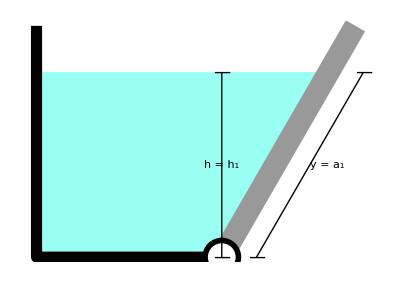

```mathematica
Module[{θ,h1,w1,w2,w3,h,a2,col,δ1,δ2},
θ=60°;
h1=4;h=5;a2=8;
w1=4;w2=h/Tan[θ];w3=h1/Tan[θ];
col=RGBColor[0.6,1,0.95];
δ1=0.75;δ2=0.1;

Graphics[{
{FaceForm@col,Polygon[{{0,h1},{0,0},{w1,0},{w1+h1/Sin[θ]*Cos[θ],h1}}]},
{Thickness@0.02,Line[{{0,h},{0,0},{w1,0}}]},
{Thickness@0.04,GrayLevel@0.6,CapForm@"Round",Line[{{w1,0},{w1+w2,h}}]},
{PointSize@0.07,Point@#,White,PointSize@0.05,Point@#}&@{w1,0},

Line[{{w1+δ1,0},{w1+w3+δ1,h1}}],
Text[Style["—",17],#]&/@{{w1+δ1,0},{w1+w3+δ1,h1}},
Text[Framed[Style[Row@{Style["y",Italic]," = ",Subscript[Style["a",Italic],1]},17],Background->White,FrameStyle->None],{2*w1+w3+2*δ1,h1}/2,{-0.5,0}],

Line[{{w1,0},{w1,h1}}],Text[Style["—",17],{w1,#}]&/@{0,h1},
Text[Framed[Style[Row@{Style["h",Italic]," = ",Subscript[Style["h",Italic],1]},17],Background->col,FrameStyle->None],{w1,h1/2}]
}]
]
```